## process saved results

```mathematica
<<"C:\\Users\\aliha\\Desktop\\optic flow\\pyramidal-KLT.m";
<<"C:\\Users\\aliha\\Desktop\\optic flow\\VectorFieldOperations.m";
```

### @C10

```mathematica
DumpGet["C:\\Users\\aliha\\Desktop\\optic flow\\sim1.mx"];
```

```mathematica
images=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\C10 - cropped.tif"];
```

```mathematica
image=ImageAdjust@images[[Ceiling[Length[images]/2]]];
```

```mathematica
meanflow=meanFlowField[sim];
```

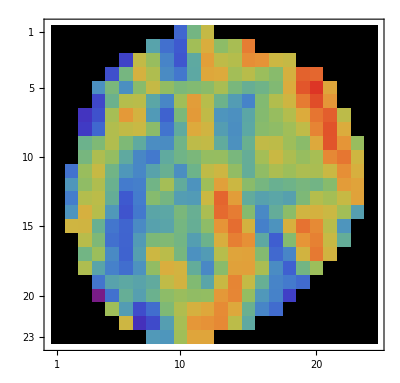
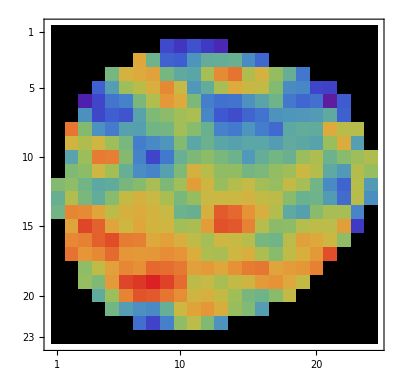
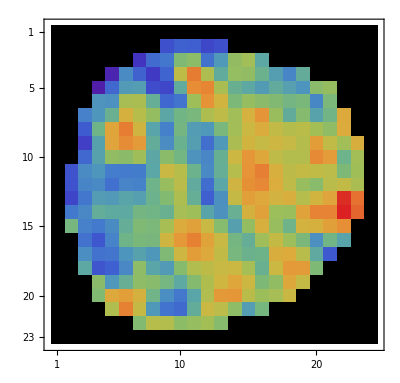
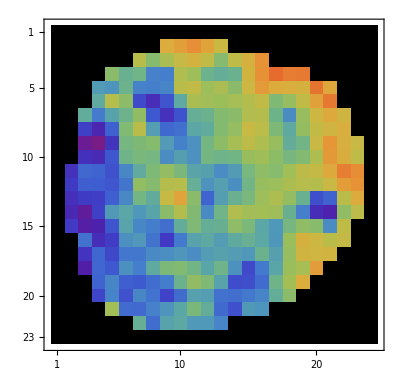
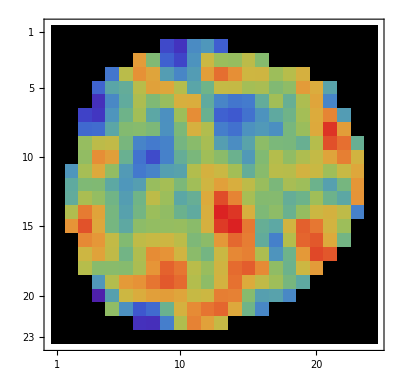
{xx→-Graphics-,yy→-Graphics-,yx→-Graphics-,xy→-Graphics-,ww→-Graphics-,trace→-Graphics-}

```mathematica
{DVxx,DVyy,DVyx,DVxy,DVww,trace,array}=velocityGrad[OptionValue[KLTracker,"dgrid"],meanflow];
```

```mathematica
(*plotVectorField[meanflow,image]*)
```

```mathematica
{graphicsPrimitive,meanflowRot}=SRMeasures[image,meanflow,DVxx,DVyy,DVxy,array];
```

```mathematica
Graphics[graphicsPrimitive,Frame->True,FrameTicks->None,Axes->{False,False}]
```

-Graphics-

```mathematica
plotStreamField[meanflowRot,image]
```

-Graphics-

```mathematica
plotSRField[graphicsPrimitive,meanflowRot,image]
```

-Graphics-

### @2

```mathematica
DumpGet["C:\\Users\\aliha\\Desktop\\optic flow\\sim2.mx"];
```

```mathematica
<<"C:\\Users\\aliha\\Desktop\\optic flow\\pyramidal-KLT.m";
<<"C:\\Users\\aliha\\Desktop\\optic flow\\VectorFieldOperations.m";
```

```mathematica
images=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\F10 - cropped.tif"];
```

```mathematica
image=ImageAdjust@images[[3Ceiling[Length[images]/4]]];
```

```mathematica
meanflow=meanFlowField[sim];
```

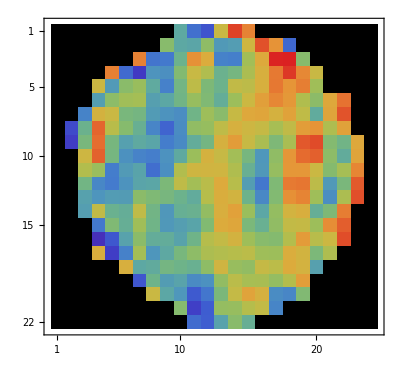
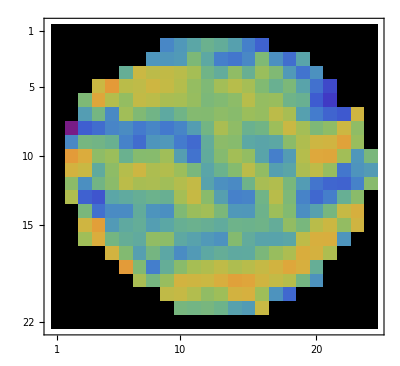
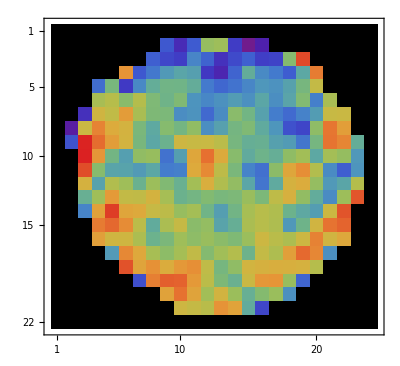
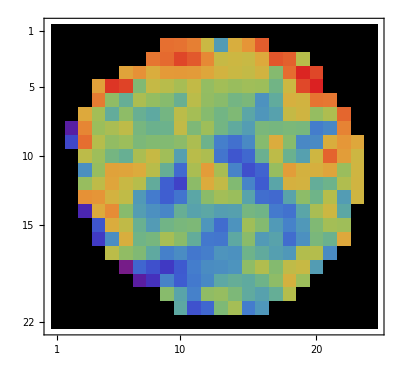
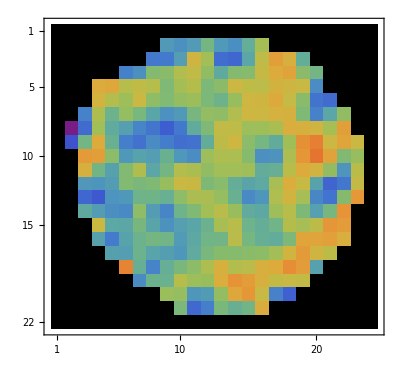
{xx→-Graphics-,yy→-Graphics-,yx→-Graphics-,xy→-Graphics-,ww→-Graphics-,trace→-Graphics-}

```mathematica
{DVxx,DVyy,DVyx,DVxy,DVww,trace,array}=velocityGrad[OptionValue[KLTracker,"dgrid"],meanflow];
```

```mathematica
plotVectorField[meanflow,image]
```

```mathematica
{graphicsPrimitive,meanflowRot}=SRMeasures[image,meanflow,DVxx,DVyy,DVxy,array];
```

```mathematica
Graphics[graphicsPrimitive,Frame->True,FrameTicks->None,Axes->{False,False}]
```

-Graphics-

```mathematica
plotStreamField[meanflowRot,image]
```

-Graphics-

```mathematica
plotSRField[graphicsPrimitive,meanflowRot,image]
```

-Graphics-

### @3

```mathematica
<<"C:\\Users\\aliha\\Desktop\\optic flow\\pyramidal-KLT.m";
<<"C:\\Users\\aliha\\Desktop\\optic flow\\VectorFieldOperations.m";
```

```mathematica
DumpGet["C:\\Users\\aliha\\Desktop\\optic flow\\sim3-filter20.mx"];
```

```mathematica
images=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\D11 - cropped.tif"];
```

```mathematica
image=ImageAdjust@images[[4Ceiling[Length[images]/6]]];
```

```mathematica
meanflow=meanFlowField[sim];
```

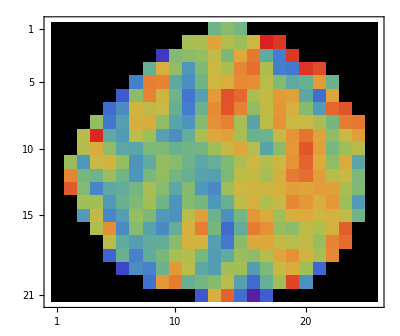
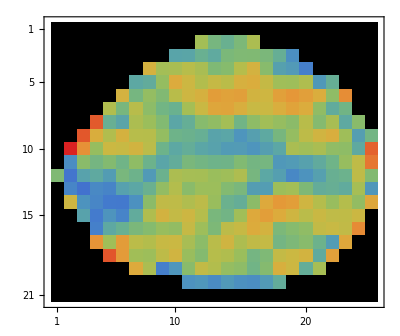
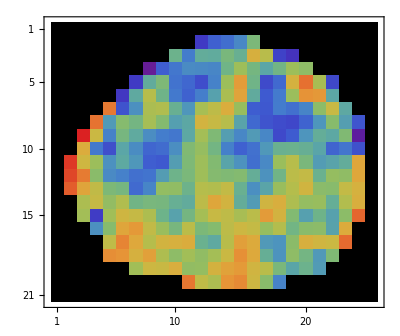
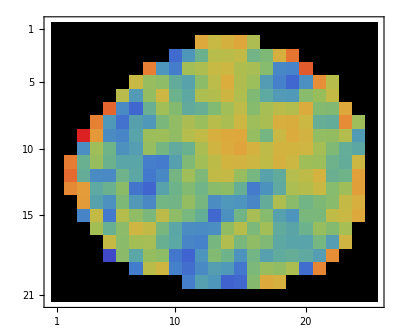
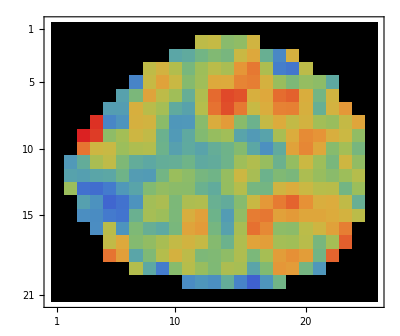
{xx→-Graphics-,yy→-Graphics-,yx→-Graphics-,xy→-Graphics-,ww→-Graphics-,trace→-Graphics-}

```mathematica
{DVxx,DVyy,DVyx,DVxy,DVww,trace,array}=velocityGrad[OptionValue[KLTracker,"dgrid"],meanflow];
```

```mathematica
plotVectorField[meanflow,image]
```

```mathematica
{graphicsPrimitive,meanflowRot}=SRMeasures[image,meanflow,DVxx,DVyy,DVxy,array];
```

```mathematica
Graphics[graphicsPrimitive,Frame->True,FrameTicks->None,Axes->{False,False}]
```

-Graphics-

```mathematica
plotStreamField[meanflowRot,image]
```

-Graphics-

```mathematica
plotSRField[graphicsPrimitive,meanflowRot,image]
```

-Graphics-